# Helmholtz equation in spherical coordinates

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","./spectral.m"];
Needs["sprouts`","./sprouts.m"];
```

```mathematica
ℒ={ϕ[0,0]''[r]+2/r ϕ[0,0]'[r]-(0(0+1))/r^2 ϕ[0,0][r]==-λ ϕ[0,0][r],ϕ[2,2]''[r]+2/r ϕ[0,2]'[r]-(2(2+1))/r^2 ϕ[2,2][r]==-λ ϕ[2,2][r]};
ℬ={ϕ[0,0][1]==0,ϕ[2,2][1]==0};
𝒱={ϕ[0,0],ϕ[2,2]};
```

```mathematica
catchErrors[expr_]:=Catch[expr/. HoldPattern[Message[msg_,___]]:>Throw[$MessageList]];
```

```mathematica
result=Trace[catchErrors[SproutsFun[Join[ℒ,ℬ],𝒱,{r,0,1},10,eigenvalue->λ]]];
```

partition of the spatial domain :  {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  10x10

{Band[{5,6}]→{SparseArray[…]}}

SparseArray[…]

{Band[{1,1}]→{SparseArray[…]}}

SparseArray[…]

{Band[{1,1}]→{SparseArray[…]},Band[{5,6}]→{SparseArray[…]}}

SparseArray[…]

{Band[{1,1}]→{SparseArray[…]},Band[{5,6}]→{SparseArray[…]}}

SparseArray[…]

{}

{}

```mathematica
(** optimised function to build sparsearray iteratively  **)
SetAttributes[BuildSparseIterate,HoldFirst];
BuildSparseIterate[Band[{i_Integer,j_Integer}]->{SparseArray[Automatic,{nbrows_Integer,nbcols_Integer},zero_,{1,{cumulnbelem_List,listcol_List},elem_List}]},{maxrows_Integer,maxcols_Integer}]:=
SparseArray[Automatic,{maxrows,maxcols},0,{1,{ConstantArray[0,i-1]~Join~cumulnbelem~Join~ConstantArray[Last[cumulnbelem],maxrows-i-nbrows+1],listcol+j-1},elem}];
```

```mathematica
tab={Band[{1,1}]->{SparseArray[…]},Band[{5,6}]->{SparseArray[…]}};
```

```mathematica
BuildSparseIterate[#,{8,10}]&/@tab
```

{SparseArray[…],SparseArray[…]}

```mathematica
SparseArray[tab,{4,5}]
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,0,1},10,eigenvalue->λ]
```

partition of the spatial domain :  {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  5x5

{SparseArray[…],SparseArray[…]}

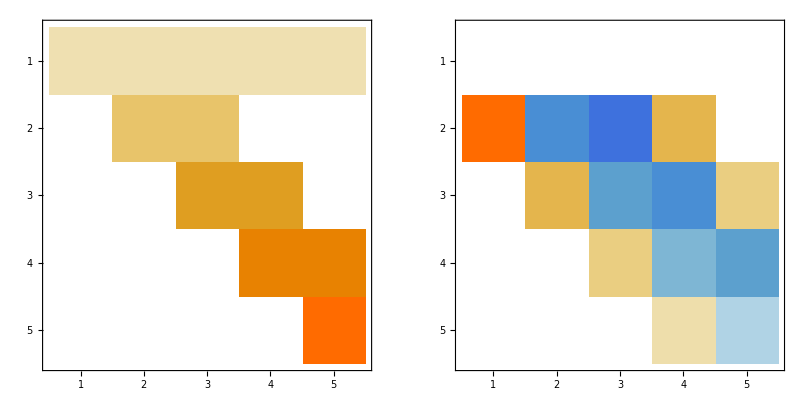

```mathematica
GraphicsRow[MatrixPlot/@A]
```

```mathematica
Sort@Eigenvalues[{A⟦1⟧,-A⟦2⟧}]//Sqrt
```

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496,21.9911,25.1327,28.2743,31.4167,34.5536,37.8035,41.3975,46.7313,53.6365,65.9317,82.7851,123.663,201.053,∞}

```mathematica
(*analytical solutions *)
Table[BesselJZero[1/2,i],{i,1,20}]//N
```

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496,21.9911,25.1327,28.2743,31.4159,34.5575,37.6991,40.8407,43.9823,47.1239,50.2655,53.4071,56.5487,59.6903,62.8319}